# 2019-2020 nCov-2 以色列和巴勒斯坦疫情地图

## 2019-2020 nCov-2 Outbreak in Israel and Palestine

### 更新时间/Time of Update

```mathematica
LocalTime[]
```

Fri 6 Mar 2020 22:00:18GMT+2.

### 覆盖范围和输入病例汇总/Covered Area and Sources of Imported Cases

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]]},GeoBackground -> None,ImageSize->100];
cc=GeoListPlot[{Entity["Country","Spain"],Entity["Country","Switzerland"],Entity["Country","Italy"],Entity["Country","Greece"],Entity["Country","Austria"],Entity["Country","UnitedStates"],Entity["Country","Japan"]},ImageSize->500];
Grid[{{tt,cc}}]
```

-Graphics- | -Graphics-

### 强制14天隔离国家/List of Countries Involved in Mandatory 14-Days Quarantine

```mathematica
cc=GeoListPlot[{Entity["Country","China"],Entity["Country","SouthKorea"],Entity["Country","Italy"],Entity["Country","France"],Entity["Country","Switzerland"],Entity["Country","Spain"],Entity["Country","Andorra"],Entity["Country","SanMarino"],Entity["Country","Austria"],Entity["Country","Japan"],Entity["Country","Singapore"],Entity["Country","Thailand"],Entity["Country","Germany"]},ImageSize->500];
Grid[{{cc},{Text[Style["China/Hong Kong/Macau, Korea, Italy, France, Switzerland, Spain, Andorra, SanMarino, Austria, Japan, Singapore, Thailand, Germany",TextAlignment->Top]]}},Alignment->{{Center},{Top}},Frame->None]
```

-Graphics-
China/Hong Kong/Macau, Korea, Italy, France, Switzerland, Spain, Andorra, SanMarino, Austria, Japan, Singapore, Thailand, Germany

## 近期病例

## 法国游客/The “French Tourist”

### 说明

游客回到法国后被确诊
A tourist after returning to France found positive for the new Corona virus

### 暴露历史/Exposure History

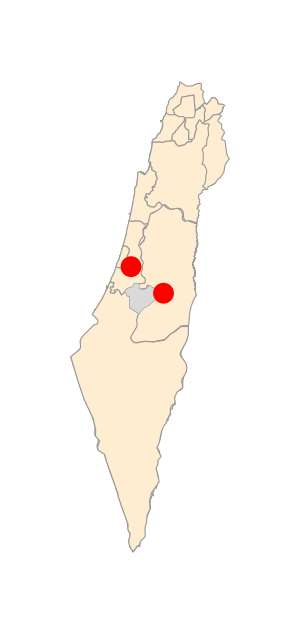
Date | Time | English | 中文 | Tel Aviv | 
02Mar2020 | 13:00- | Transavia 3933 back to France |  | -Graphics- | -Graphics-
02Mar2020 | 12:30-13:00 | Train from Jerusalem to Ben Gurion Airport |  |  | 
02Mar2020 | 10:30-12:00 | Hillel Cafe(Ramat Beit HaKerem) at Avizohar St 8, Jerusalem, Israel |  |  | 
01Mar2020 | 20:00-23:00 | Family Party at Rambam Synagogue, Amatsya St 4, Jerusalem, Israel |  |  | 
01Mar2020 | 13:30-14:00 | Train from Ben Gurion Airport to Jerusalem |  |  | 
01Mar2020 | -12:30 | Transavia 3930 to Israel |  |  |

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[Entity["AdministrativeDivision",{"Jerusalem","Israel"}]],Red,PointSize[0.05],Point[{Entity["City",{"Jerusalem","Jerusalem","Israel"}],Entity["Airport","LLBG"]}]},GeoBackground ->None,ImageSize->300];
cc=GeoListPlot[{Entity["City",{"Jerusalem","Jerusalem","Israel"}],GeoPosition[{31.774696,35.187087}],GeoPosition[{31.762072,35.215392}]},GeoLabels->True,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","Tel Aviv"},
{"02Mar2020","13:00-","Transavia 3933 back to France","",tt,cc},
{"02Mar2020","12:30-13:00","Train from Jerusalem to Ben Gurion Airport","",SpanFromAbove,SpanFromAbove},
{"02Mar2020","10:30-12:00","Hillel Cafe(Ramat Beit HaKerem) at Avizohar St 8, Jerusalem, Israel","",SpanFromAbove,SpanFromAbove},
{"01Mar2020","20:00-23:00","Family Party at Rambam Synagogue, Amatsya St 4, Jerusalem, Israel","",SpanFromAbove,SpanFromAbove},
{"01Mar2020","13:30-14:00","Train from Ben Gurion Airport to Jerusalem","",SpanFromAbove,SpanFromAbove},
{"01Mar2020","-12:30","Transavia 3930 to Israel","",SpanFromAbove,SpanFromAbove}},Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,25,30}}]
```

## 意大利游客/The “Italian Tourist”

### 说明

游客回到意大利后被确诊
A tourist after returning to Italy found positive for the new Corona virus

### 暴露历史/Exposure History

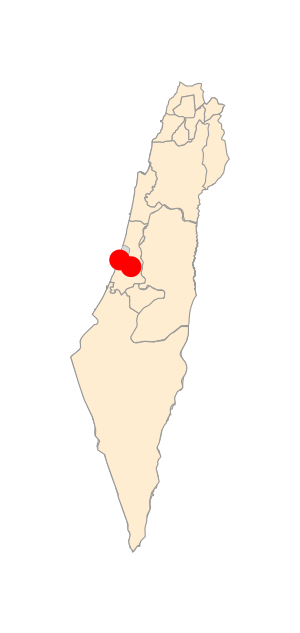
Date | Time | English | 中文 | Tel Aviv | 
25Feb2020 | 05:15- | Alitalia AZ809 Tel Aviv-Italy |  | -Graphics- | -Graphics-
24Feb2020 | 22:30-02:45am+1 | ANIMAR Restaurant 1st Floor Dan Tel Aviv hotel, Tel Aviv |  |  | 
24Feb2020 | 08:15-14:00 | 16th Floor, 21 HaArba'a Street, Tel Aviv |  |  | 
24Feb2020 | 07:00-08:00 | Taxi from Dan Tel Aviv Hotel to 21 HaArba'a Street, Tel Aviv |  |  | 
24Feb2020 | 07:00-08:00 | Breakfast at Dan Tel Aviv hotel, Tel Aviv |  |  | 
23Feb2020 | 18:30-21:30 | ANIMAR Restaurant 1st Floor Dan Tel Aviv hotel, Tel Aviv |  |  |

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[Entity["AdministrativeDivision",{"TelAviv","Israel"}]],GeoPath[{Entity["City",{"TelAvivYafo","TelAviv","Israel"}],Entity["Airport","LLBG"]},"Geodesic"],Red,PointSize[0.05],Point[{Entity["City",{"TelAvivYafo","TelAviv","Israel"}],Entity["Airport","LLBG"]}]},GeoBackground->None,ImageSize->300];
cc=GeoListPlot[{Entity["City",{"TelAvivYafo","TelAviv","Israel"}],GeoPosition[{32.079560,34.767842}],GeoPosition[{32.070462,34.786938}]},GeoLabels->True,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","Tel Aviv"},
{"25Feb2020","05:15-","Alitalia AZ809 Tel Aviv-Italy","",tt,cc},
{"24Feb2020","22:30-02:45am+1","ANIMAR Restaurant 1st Floor Dan Tel Aviv hotel, Tel Aviv","",SpanFromAbove,SpanFromAbove},
{"24Feb2020","08:15-14:00","16th Floor, 21 HaArba'a Street, Tel Aviv","",SpanFromAbove,SpanFromAbove},
{"24Feb2020","07:00-08:00","Taxi from Dan Tel Aviv Hotel to 21 HaArba'a Street, Tel Aviv","",SpanFromAbove,SpanFromAbove},
{"24Feb2020","07:00-08:00","Breakfast at Dan Tel Aviv hotel, Tel Aviv","",SpanFromAbove,SpanFromAbove},
{"23Feb2020","18:30-21:30","ANIMAR Restaurant 1st Floor Dan Tel Aviv hotel, Tel Aviv","",SpanFromAbove,SpanFromAbove}},Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,25,30}}]
```

## 第21例/Case 21

### 说明

欧洲输入病例
Travel history in Europe

### 暴露历史/Exposure History

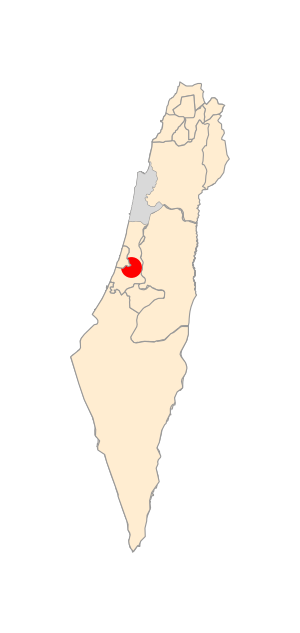
Date | Time | English | 中文 | Haifa District
01Mar2020 | 10:25- | Austrian OS857 Vienna-Tel Aviv |  | -Graphics-
01Mar2020 | 08:05- | Austrian OS916 Innsbruck-Vienna |  | 
25Feb2020 | 20:35- | Austrian OS913 Vienna-Innsbruck |  | 
25Feb2020 | 16:10- | Austrian OS858 Tel Aviv-Vienna |  |

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[Entity["AdministrativeDivision",{"Haifa","Israel"}]],Red,PointSize[0.05],Point[{Entity["Airport","LLBG"]}]},GeoBackground -> None,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","Haifa District"},
{"01Mar2020","10:25-","Austrian OS857 Vienna-Tel Aviv","",tt},
{"01Mar2020","08:05-","Austrian OS916 Innsbruck-Vienna","",SpanFromAbove},
{"25Feb2020","20:35-","Austrian OS913 Vienna-Innsbruck","",SpanFromAbove},
{"25Feb2020","16:10-","Austrian OS858 Tel Aviv-Vienna","",SpanFromAbove}},Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,35}}]
```

## 第20例/Case 20

### 说明

欧洲输入病例，参加马德里的Super Classico
Travel history in Europe for the “Super Classico” in Madrid

### 暴露历史/Exposure History

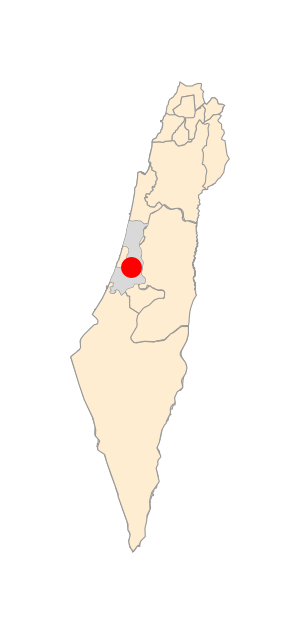
Date | Time | English | 中文 | HaMerkaz
03Mar2020 | -02:35 | Brussel Airlines SN3293 Brussels-Tel Aviv |  | -Graphics-
02Mar2020 | 21:15- | Brussel Airlines SN3728 Madrid-Brussels |  | 
28Feb2020 | 08:00- | Arkia IZ231 |  |

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[Entity["AdministrativeDivision",{"Hamerkaz","Israel"}]],Red,PointSize[0.05],Point[{Entity["Airport","LLBG"]}]},GeoBackground -> None,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","HaMerkaz"},
{"03Mar2020","-02:35","Brussel Airlines SN3293 Brussels-Tel Aviv","",tt},
{"02Mar2020","21:15-","Brussel Airlines SN3728 Madrid-Brussels","",SpanFromAbove},
{"28Feb2020","08:00-","Arkia IZ231","",SpanFromAbove}},Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,35}}]
```

## 第19例/Case 19

### 说明

欧洲输入病例
Travel history in Europe

### 暴露历史/Exposure History

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[Entity["AdministrativeDivision",{"Hamerkaz","Israel"}]],Red,PointSize[0.05],Point[{Entity["Airport","LLBG"]}]},GeoBackground -> None,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","HaMerkaz"},
{"04Mar2020","22:40-02:00","El Al flight LX256 Zürich-Tel Aviv","",tt},
{"27Feb2020","05:20-08:40","El Al/Swiss flight LX257 Tel Aviv-Zürich","",SpanFromAbove}},Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,35,35}}]
```

Date | Time | English | 中文 | HaMerkaz
04Mar2020 | 22:40-02:00 | El Al flight LX256 Zürich-Tel Aviv |  | -Graphics-
27Feb2020 | 05:20-08:40 | El Al/Swiss flight LX257 Tel Aviv-Zürich |  |

## 第18-19例/Case 18-19

### 说明

欧洲输入病例
Travel history in Europe

### 暴露历史/Exposure History

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[Entity["AdministrativeDivision",{"Hamerkaz","Israel"}]],Red,PointSize[0.05],Point[{Entity["Airport","LLBG"]}]},GeoBackground -> None,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","HaMerkaz"},
{"04Mar2020","","#19 Return from Zürich","",tt},
{"27Feb2020","","#18 Return from Madrid","",SpanFromAbove}},Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,35,35}}]
```

Date | Time | English | 中文 | HaMerkaz
04Mar2020 |  | #19 Return from Zürich |  | -Graphics-
27Feb2020 |  | #18 Return from Madrid |  |

## 第17例/Case 17

### 说明

欧洲输入病例
Travel history in Europe

### 暴露历史/Exposure History

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[Entity["AdministrativeDivision",List["HaMerkaz","Israel"]]],Red,PointSize[0.05],Point[{Entity["Airport","LLBG"]}]},GeoBackground -> None,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","HaMerkaz"},{"29Feb2020","12:20pm","EasyJet EJ3342: Venice to Ben Gurion","EasyJet EJ3342航班，2020年2月29日从威尼斯到本古里安机场",tt},{"","","Self-quarantine since entry","自入境以来自我隔离",SpanFromAbove}},Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,35,35}}]
```

Date | Time | English | 中文 | HaMerkaz
29Feb2020 | 12:20pm | EasyJet EJ3342: Venice to Ben Gurion | EasyJet EJ3342航班，2020年2月29日从威尼斯到本古里安机场 | -Graphics-
 |  | Self-quarantine since entry | 自入境以来自我隔离 |

## 第16例/Case 16

### 说明

东耶路撒冷居民，旅游车司机，接待过来自西班牙、德国、希腊的游客
Resident of East Jerusalem who drove the tourists from Spain, Germany, Greece

### 暴露历史/Exposure History

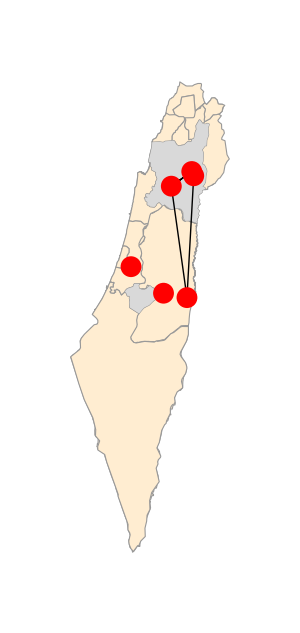
Date | Time | English | 中文 | East Jerusalem, HaTzafon, Qumran
04Mar2020 | 18:30-20:00 | Restel Hotel, Tiberias |  | -Graphics-
29Feb2020 | 12:00-13:00 | Qumran Restaurant, Qumran |  | 
28Feb2020 | 18:00-08:00am+1 | Golden Crown Old City, Nazareth |  | 
27Feb2020 | 18:00-08:00am+1 | Golden Crown Old City, Nazareth |  | 
27Feb2020 | 12:30-15:00 | Dalia(דליה) Restaurant, Migdal |  | 
26Feb2020 | 18:00-08:00am+1 | Golden Crown Old City, Nazareth |  |

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[Entity["AdministrativeDivision",{"Northern","Israel"}]],GeoStyling[LightGray],Polygon[Entity["AdministrativeDivision",{"Jerusalem","Israel"}]],GeoPath[{Entity["City",{"Nazerat","Northern","Israel"}],GeoPosition[{32.836720,35.509808}],Entity["City",{"Nazerat","Northern","Israel"}],GeoPosition[{31.741458,35.460543}],Entity["City",{"Tiberias","Northern","Israel"}]},"Geodesic"],Red,PointSize[0.05],Point[{Entity["City",{"Tiberias","Northern","Israel"}],Entity["City",{"Jerusalem","Jerusalem","Israel"}],GeoPosition[{32.836720,35.509808}],Entity["City",{"Nazerat","Northern","Israel"}],Entity["Airport","LLBG"],GeoPosition[{31.741458,35.460543}]}]},GeoBackground -> None,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","East Jerusalem, HaTzafon, Qumran"},{"04Mar2020","18:30-20:00","Restel Hotel, Tiberias","",tt},
{"29Feb2020","12:00-13:00","Qumran Restaurant, Qumran","",SpanFromAbove},
{"28Feb2020","18:00-08:00am+1","Golden Crown Old City, Nazareth","",SpanFromAbove},
{"27Feb2020","18:00-08:00am+1","Golden Crown Old City, Nazareth","",SpanFromAbove},
{"27Feb2020","12:30-15:00","Dalia(דליה) Restaurant, Migdal","",SpanFromAbove},
{"26Feb2020","18:00-08:00am+1","Golden Crown Old City, Nazareth","",SpanFromAbove}},Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,35,35}}]
```

## 伯利恒的7名巴勒斯坦人/7 Palestinians from Bethlehem

### 暴露历史/Exposure History

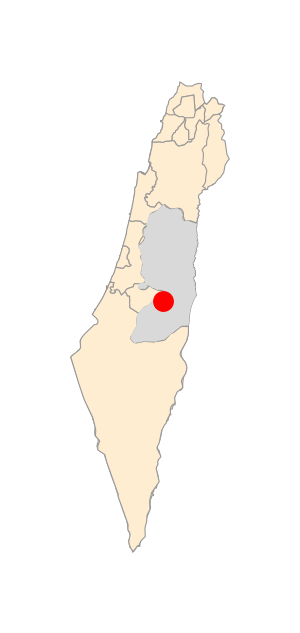
|  | English | 中文 | West Bank, Bethlehem
 |  | Unknown | 不明 | -Graphics-

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[Entity["Country","WestBank"]],Red,PointSize[0.05],Point[{Entity["City",{"BaytLahm","Bethlehem","WestBank"}]}]},GeoBackground -> None,ImageSize->300];
TextGrid[{{"","","English","中文","West Bank, Bethlehem"},{"","","Unknown","不明",tt}},Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,35,35}}]
```

## 希腊游客/Greek Tourists

### 暴露历史/Exposure History

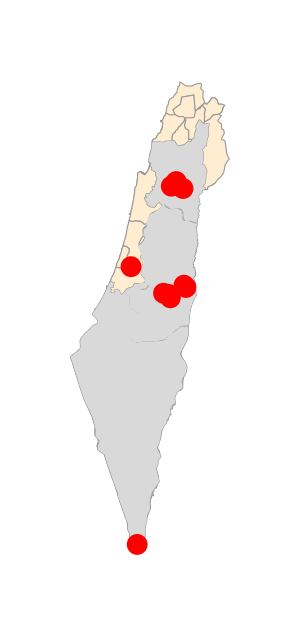
Date | Time | English | 中文 | Jerusalem, Mt Tabor Area, Jericho, Eilat
27Feb2020 |  | The group left Israel on Aegean Airlines flight number A3925 | 乘坐爱琴海航空A3925离开以色列 | -Graphics-
27Feb2020 | 16:00-16:40 |  St. George's Church, Lod | 卢德St. George教堂 | 
26Feb2020 | 18:40-03:10 | Church of the Holy Sepulcher Jerusalem | 圣墓教堂，耶路撒冷 | 
26Feb2020 | 13:10-14:20 | Deir Hajala, near Jericho | Deir Hajala，耶利哥附近 | 
26Feb2020 | 12:30 | Zakaa(אקז) Church | Zakaa(אקז)教堂 | 
26Feb2020 | 11:00 | Qarantal Monastery/Monastery of the Temptation, Jericho | Qarantal修道院/试探教堂，耶利哥 | 
25Feb2020 | 12:30 | Mar Saba, West Bank | 约旦河西岸Mar Saba | 
25Feb2020 | 10:30-11:45 | Church of Martha, Mary and Lazarus, al-Eizariya
 | 拉撒路修道院，伯大尼 | 
25Feb2020 | 08:00-10:00 | St. George/Mar Jaris Monastery, Aqabat Jabr
 | St. George/Mar Jaris修道院，Aqabat Jabr | 
24Feb2020 | 13:30-17:00 | Tomb of Mary and Church of All Nations,Jerusalem | 玛丽亚墓和万国教堂，耶路撒冷 | 
24Feb2020 | 08:00-10:30 | Mar Saba Monastery
 | Mar Saba修道院 | 
23Feb2020 | 18:00-18:30 | Yotvata(התבטוי) Restaurant, near Eilat
 | Yotvata(התבטוי)餐馆，埃拉特附近 | 
23Feb2020 | 15:30-17:30 | Eilat Observatory, Eilat
 | 埃拉特海景平台，埃拉特 | 
21Feb2020 | 10:30-11:00 | Yotvata(התבטוי) Restaurant, near Eilat
 | Yotvata(התבטוי)餐馆，埃拉特附近 | 
21Feb2020 | 7:30-8:00 | Dead Sea, Ein Boqeq
 | 死海，Ein Boqeq | 
20Feb2020 | 16:30-17:30 | Yardenit Baptism Site, Beit Yareh
 | Yardenit洗礼点, Beit Yareh | 
20Feb2020 | 15:00-15:30 | Ein Sheva/Tabigha
 | Ein Sheva/Tabigha | 
20Feb2020 | 12:00 | Greek Orthodox Church in Kfar Kana
 | Kfar Kana希腊正教会 | 
20Feb2020 | 11:00 | Basilica of the Annunciation, Nazareth
 | 圣母领报堂，拿撒勒 | 
20Feb2020 | 09:00-10:30 | Mount Tabor Monastery
 | 耶稣显圣容教堂，他泊山 |

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[{Entity["AdministrativeDivision",{"Northern","Israel"}],Entity["AdministrativeDivision",{"Jerusalem","Israel"}],Entity["Country","WestBank"],Entity["AdministrativeDivision",{"Hadarom","Israel"}]}],Red,PointSize[0.05],Point[{Entity["City",{"Nazerat","Northern","Israel"}],Entity["City",{"Jerusalem","Jerusalem","Israel"}],Entity["City",{"KafarKanna","Northern","Israel"}],Entity["City",{"Elat","Hadarom","Israel"}],Entity["City",{"AlAyzariyah","Jerusalem","WestBank"}],Entity["City",{"Ariha","Jericho","WestBank"}],Entity["City",{"KefarTavor","Northern","Israel"}],Entity["City",{"AqbahJabbar","Jericho","WestBank"}],Entity["City",{"AlUbaydiyah","Bethlehem","WestBank"}],Entity["Airport","LLBG"]}]},GeoBackground -> None,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","Jerusalem, Mt Tabor Area, Jericho, Eilat"},{"27Feb2020","","The group left Israel on Aegean Airlines flight number A3925","乘坐爱琴海航空A3925离开以色列",tt},{"27Feb2020","16:00-16:40"," St. George's Church, Lod","卢德St. George教堂",SpanFromAbove},
{"26Feb2020","18:40-03:10","Church of the Holy Sepulcher Jerusalem","圣墓教堂，耶路撒冷",SpanFromAbove},
{"26Feb2020","13:10-14:20","Deir Hajala, near Jericho","Deir Hajala，耶利哥附近",SpanFromAbove},
{"26Feb2020","12:30","Zakaa(אקז) Church","Zakaa(אקז)教堂",SpanFromAbove},
{"26Feb2020","11:00","Qarantal Monastery/Monastery of the Temptation, Jericho","Qarantal修道院/试探教堂，耶利哥",SpanFromAbove},
{"25Feb2020","12:30","Mar Saba, West Bank","约旦河西岸Mar Saba",SpanFromAbove},
{"25Feb2020","10:30-11:45","Church of Martha, Mary and Lazarus, al-Eizariya
","拉撒路修道院，伯大尼",SpanFromAbove},
{"25Feb2020","08:00-10:00","St. George/Mar Jaris Monastery, Aqabat Jabr
","St. George/Mar Jaris修道院，Aqabat Jabr",SpanFromAbove},
{"24Feb2020","13:30-17:00","Tomb of Mary and Church of All Nations,Jerusalem","玛丽亚墓和万国教堂，耶路撒冷",SpanFromAbove},
{"24Feb2020","08:00-10:30","Mar Saba Monastery
","Mar Saba修道院",SpanFromAbove},
{"23Feb2020","18:00-18:30","Yotvata(התבטוי) Restaurant, near Eilat
","Yotvata(התבטוי)餐馆，埃拉特附近",SpanFromAbove},
{"23Feb2020","15:30-17:30","Eilat Observatory, Eilat
","埃拉特海景平台，埃拉特",SpanFromAbove},
{"21Feb2020","10:30-11:00","Yotvata(התבטוי) Restaurant, near Eilat
","Yotvata(התבטוי)餐馆，埃拉特附近",SpanFromAbove},
{"21Feb2020","7:30-8:00","Dead Sea, Ein Boqeq
","死海，Ein Boqeq",SpanFromAbove},
{"20Feb2020","16:30-17:30","Yardenit Baptism Site, Beit Yareh
","Yardenit洗礼点, Beit Yareh",SpanFromAbove},
{"20Feb2020","15:00-15:30","Ein Sheva/Tabigha
","Ein Sheva/Tabigha",SpanFromAbove},
{"20Feb2020","12:00","Greek Orthodox Church in Kfar Kana
","Kfar Kana希腊正教会",SpanFromAbove},
{"20Feb2020","11:00","Basilica of the Annunciation, Nazareth
","圣母领报堂，拿撒勒",SpanFromAbove},
{"20Feb2020","09:00-10:30","Mount Tabor Monastery
","耶稣显圣容教堂，他泊山",SpanFromAbove}
},
Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,35,35}}]
```

## 纽约游客/The “New York Tourist”

### 暴露历史/Exposure History

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[{Entity["AdministrativeDivision",{"Jerusalem","Israel"}]}],Red,PointSize[0.05],Point[{Entity["City",{"Jerusalem","Jerusalem","Israel"}],Entity["Airport","LLBG"]}]},GeoBackground -> None,ImageSize->300];
cc=GeoListPlot[Join[{Entity["City",{"Jerusalem","Jerusalem","Israel"}]},GeoPosition/@{{31.763676,35.219286},{31.789140,35.203134},{31.767708,35.224322},{31.753059,35.213825},{31.782195,35.221448},{31.767708,35.224322},{31.781794,35.218560},{31.781654,35.216718},{31.744442,35.216431}}],GeoLabels->True,ImageSize->300];TextGrid[{{"Date","Time","English","中文","Jerusalem, Hebron Road"},{"27Feb2020","20:30","Train Jerusalem-Ben Gurion Airport","",tt,cc},
{"27Feb2020","19:30","Egged 74 Hebron Road-Central Bus Station Jerusalem","",SpanFromAbove,SpanFromAbove},
{"27Feb2020","11:00-13:00","Coffee Shop at 36 Emek Refa'im St, Jerusalem","",SpanFromAbove,SpanFromAbove},
{"27Feb2020","10:00","Egged 74 Hebron Road-Talpiot","",SpanFromAbove,SpanFromAbove},
{"26Feb2020","11:30-14:00","Hadar Mall Jerusalem, FOX Home","",SpanFromAbove,SpanFromAbove},
{"26Feb2020","09:00-10:00","Mizrahi Tefahot Bank at 9 Heleni HaMalka Street","",SpanFromAbove,SpanFromAbove},
{"25Feb2020","","David Remez 4, Jerusalem","",SpanFromAbove,SpanFromAbove},
{"25Feb2020","14:00-15:00","KITCHEN STATION Restaurant","",SpanFromAbove,SpanFromAbove},
{"24Feb2020","17:00-19:00","Hadar Mall, Pierre Koenig 26 Jerusalem","",SpanFromAbove,SpanFromAbove},
{"24Feb2020","","Egged 74 at 15 King George to Hebron Road","",SpanFromAbove,SpanFromAbove},
{"24Feb2020","13:00-15:00","Cafe Rimon on Ben Yehuda, Jerusalem","",SpanFromAbove,SpanFromAbove},
{"23Feb2020","09:30","Cafe Rimon on Ben Yehuda, Jerusalem and ZARA on Mamilla Avenue","",SpanFromAbove,SpanFromAbove}
},
Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,25,29}}]
```

Date | Time | English | 中文 | Jerusalem, Hebron Road | 
27Feb2020 | 20:30 | Train Jerusalem-Ben Gurion Airport |  | -Graphics- | -Graphics-
27Feb2020 | 19:30 | Egged 74 Hebron Road-Central Bus Station Jerusalem |  |  | 
27Feb2020 | 11:00-13:00 | Coffee Shop at 36 Emek Refa'im St, Jerusalem |  |  | 
27Feb2020 | 10:00 | Egged 74 Hebron Road-Talpiot |  |  | 
26Feb2020 | 11:30-14:00 | Hadar Mall Jerusalem, FOX Home |  |  | 
26Feb2020 | 09:00-10:00 | Mizrahi Tefahot Bank at 9 Heleni HaMalka Street |  |  | 
25Feb2020 |  | David Remez 4, Jerusalem |  |  | 
25Feb2020 | 14:00-15:00 | KITCHEN STATION Restaurant |  |  | 
24Feb2020 | 17:00-19:00 | Hadar Mall, Pierre Koenig 26 Jerusalem |  |  | 
24Feb2020 |  | Egged 74 at 15 King George to Hebron Road |  |  | 
24Feb2020 | 13:00-15:00 | Cafe Rimon on Ben Yehuda, Jerusalem |  |  | 
23Feb2020 | 09:30 | Cafe Rimon on Ben Yehuda, Jerusalem and ZARA on Mamilla Avenue |  |  |

## 第15例/Case 15

### 说明

欧洲输入病例
Travel history in Europe

### 暴露历史/Exposure History

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[{Entity["AdministrativeDivision",{"TelAviv","Israel"}]}],Red,PointSize[0.05],Point[{Entity["City",{"TelAvivYafo","TelAviv","Israel"}],Entity["Airport","LLBG"]}]},GeoBackground -> None,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","Tel Aviv, Ben Gurion Airport"},{"29Feb2020","16:30","EasyJet EJU3342 Venice to Ben Gurion","EasyJet EJU3342 威尼斯到本古里安机场",tt},
{"","","Self-quarantine since entry","自入境以来自我隔离",SpanFromAbove}
},
Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,35,35}}]
```

Date | Time | English | 中文 | Tel Aviv, Ben Gurion Airport
29Feb2020 | 16:30 | EasyJet EJU3342 Venice to Ben Gurion | EasyJet EJU3342 威尼斯到本古里安机场 | -Graphics-
 |  | Self-quarantine since entry | 自入境以来自我隔离 |

## 第14例/Case 14

### 说明

本例和Red Pirate商店有关
This case is linked to the shop “Red Pirate” in Or Yehuda

### 暴露历史/Exposure History

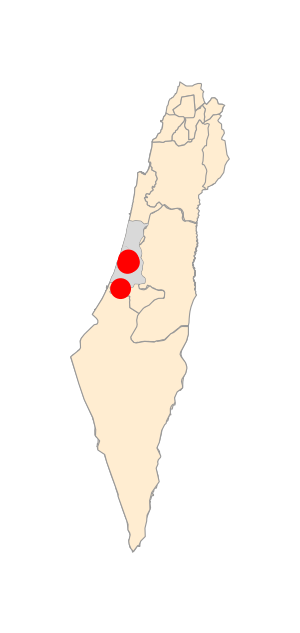
Date | Time | English | 中文 | HaMerkaz, Tel Aviv | 
28Feb2020 | Afternoon | Home quarantine |  | -Graphics- | -Graphics-
28Feb2020 | 7:30-12:00  | Avigdor Warsaw School, Kiryat Ono |  |  | 
27Feb2020 | 20:30-20:45 | Bus 55 from Kiryat Ono Mall(Levi Eshkol) to Ganei Tikva(Hari Yehuda St) |  |  | 
27Feb2020 | 18:00-20:30 | Kiryat Ono Mall, TOGO shoes , Renoir Women (Top Floor), Fox Women (Entrance), Fox Kids (Entrance) and Shufersal |  |  | 
26Feb2020 | 19:30-22:30 | Wedding at 'Harmonia BaGan' at Gedera Junction |  |  | 
26Feb2020 | 17:15-18:00 | Sports hall near Ganei Tikva Municipal Library |  |  | 
26Feb2020 | 7:30-13:00  | Avigdor Warsaw School, Kiryat Ono |  |  | 
25Feb2020 | 1/2 Hour | 'Red Pirate' Store, Or Yehuda |  |  |

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[{Entity["AdministrativeDivision",{"TelAviv","Israel"}],Entity["AdministrativeDivision",{"Hamerkaz","Israel"}]}],Red,PointSize[0.05],Point[{Entity["City",{"OrYehuda","TelAviv","Israel"}],Entity["City",{"QiryatOno","TelAviv","Israel"}],Entity["City",{"Gedera","Hamerkaz","Israel"}],Entity["City",{"GanneTiqwa","TelAviv","Israel"}]}]},GeoBackground -> None,ImageSize->300];
cc=GeoListPlot[{Entity["City",{"OrYehuda","TelAviv","Israel"}],Entity["City",{"QiryatOno","TelAviv","Israel"}],Entity["City",{"Gedera","Hamerkaz","Israel"}],Entity["City",{"GanneTiqwa","TelAviv","Israel"}],GeoPosition[{32.052848,34.855805}],GeoPosition[{32.055517,34.864360}],GeoPosition[{32.060749,34.868544}],GeoPosition[{31.803403,34.762047}],GeoPosition[{32.063855,34.872920}],GeoPosition[{32.022702,34.861795}]},GeoLabels->True,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","HaMerkaz, Tel Aviv"},
{"28Feb2020","Afternoon","Home quarantine","",tt,cc},
{"28Feb2020","7:30-12:00 ","Avigdor Warsaw School, Kiryat Ono","",SpanFromAbove,SpanFromAbove},
{"27Feb2020","20:30-20:45","Bus 55 from Kiryat Ono Mall(Levi Eshkol) to Ganei Tikva(Hari Yehuda St)","",SpanFromAbove,SpanFromAbove},
{"27Feb2020","18:00-20:30","Kiryat Ono Mall, TOGO shoes , Renoir Women (Top Floor), Fox Women (Entrance), Fox Kids (Entrance) and Shufersal","",SpanFromAbove,SpanFromAbove},
{"26Feb2020","19:30-22:30","Wedding at 'Harmonia BaGan' at Gedera Junction","",SpanFromAbove,SpanFromAbove},
{"26Feb2020","17:15-18:00","Sports hall near Ganei Tikva Municipal Library","",SpanFromAbove,SpanFromAbove},
{"26Feb2020","7:30-13:00 ","Avigdor Warsaw School, Kiryat Ono","",SpanFromAbove,SpanFromAbove},
{"25Feb2020","1/2 Hour","'Red Pirate' Store, Or Yehuda","",SpanFromAbove,SpanFromAbove}
},
Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,25,30}}]
```

## 第13例“男孩”/Case 13 “The Boy”

本例在Irus，Ness Ziona以西。在Brenner Regional School上学，与Red Pirate商店有关
This case lives in Irus, west to Ness Ziona and goes to school at the Brenner Regional School, linked to the shop “Red Pirate”.

### 暴露历史/Exposure History

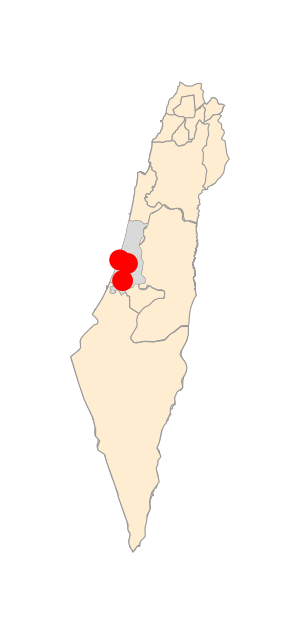
Date | Time | English | 中文 | Rehovot, Or Yehuda, Tel Aviv | 
29Feb2020 |  | Home quarantine |  | -Graphics- | -Graphics-
24Feb2020 | 20:00-22:00 | Bloomfield Stadium, Tel Aviv |  |  | 
24Feb2020-26Feb2020 |  | Brenner Regional School, Rehovot |  |  | 
23Feb2020-26Feb2020 | 16:30-21:00 | 'Red Pirate' Store, Or Yehuda |  |  |

```mathematica
tt=GeoGraphics[{GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]],GeoStyling[LightGray],Polygon[{Entity["AdministrativeDivision",{"TelAviv","Israel"}],Entity["AdministrativeDivision",{"Hamerkaz","Israel"}]}],Red,PointSize[0.05],Point[{Entity["City",{"OrYehuda","TelAviv","Israel"}],Entity["City",{"Rehovot","Hamerkaz","Israel"}],Entity["City",{"TelAvivYafo","TelAviv","Israel"}]}]},GeoBackground -> None,ImageSize->300];
cc=GeoListPlot[{Entity["City",{"OrYehuda","TelAviv","Israel"}],Entity["City",{"Rehovot","Hamerkaz","Israel"}],Entity["City",{"TelAvivYafo","TelAviv","Israel"}],GeoPosition[{32.051711,34.761871}],GeoPosition[{32.022702,34.861795}],GeoPosition[{31.868838,34.806118}],GeoPosition[{31.928799,34.777205}]},GeoLabels->True,ImageSize->300];
TextGrid[{{"Date","Time","English","中文","Rehovot, Or Yehuda, Tel Aviv"},
{"29Feb2020","","Home quarantine","",tt,cc},
{"24Feb2020","20:00-22:00","Bloomfield Stadium, Tel Aviv","",SpanFromAbove,SpanFromAbove},
{"24Feb2020-26Feb2020","","Brenner Regional School, Rehovot","",SpanFromAbove,SpanFromAbove},
{"23Feb2020-26Feb2020","16:30-21:00","'Red Pirate' Store, Or Yehuda","",SpanFromAbove,SpanFromAbove}
},
Frame->All,Background->{LightBlue,{Blue}},ItemSize->{{10,10,10,10,25,35}}]
```

## Other Cases

## Case 12

## Case 11

```mathematica
AirportData["SampleEntities"]
```

{Logan Airport,Chicago O'Hare International Airport,Spencer NOLF,Dogwood Airpark,London Heathrow Airport,Le Breuil Airport,Amsterdam Airport Schiphol,Tunis-Carthage International Airport,Kijang,Moorabbin Airport}

```mathematica
Entity["Airport","LFOQ"]//FullForm
```

Entity["Airport","LFOQ"]

```mathematica
GeoEntities[Entity["Country","Israel"],"City"]
```

{Abu Ghosh,Adi,Afula,Akko,al-Burj,al-Jalamah,al-Judayrah,Arad,Arara-BaNegev,Arara,Arrabe,Ashdod,Ashqelon,Atlit,Aydah,Azur,Baqa-Jatt,Basma,Basmat Tabun,Bat Hefer,Bat Yam,Beer Sheva,Beer Yaaqov,Beit Jann,Bene Ayish,Bene Beraq,Bet Dagan,Bet Shean,Bet Shemesh,Bet Yizhaq,Binyamina-Givat Ada,Bir El-Maksur,Bueine-Nujeidat,Buqata,Dabburiyya,Daliyat Al Karmel-Isifya,Deir Hanna,Dimona,Eilabun,Ein Mahel,Ein Naqquba,Elad,Elat,Elyakhin,Even Yehuda,Fassuta,Fureidis,Gan Ner,Ganne Tiqwa,Gan Yavne,Gedera,Givat Avni,Givatayim,Givat Ela,Givat Shemuel,Glil Yam,Hadera,Haifa,Hazor HaGelilit,Herzeliyya,Hod HaSharon,Holon,Hura,Hurfeish,Ibillin,Ibtin,Iksal,Ilut,Ir Hahamisha,Jaffa,Jaljulye,Jerusalem,Jish,Jisr Az-Zarqa,Judeide-Maker,Kaabiyye-Tabbash-Hajaj,Kabul,Kafar Bara,Kafar Kama,Kafar Kanna,Kafar Manda,Kafar Misr,Kafar Qara,Kafar Qasem,Kafar Yasif,Kaokab Abu Al-Hija,Karme Yosef,Karmiel,Kefar Habad,Kefar Sava,Kefar Shemaryahu,Kfar Tavor,Kefar Weradim,Kefar Yona,Kisra-Sumei,Kokhav Yair,Kuseife,Lappid,Laqye,Lehavim,Lod,Maale Iron,Maalot-Tarshiha,Majdal Shams,Masade,Mashhed,Mattan,Mazkeret Batya,Mazraa,Merkaz Shappira,Metar,Mevasserat Ziyyon,Mielya,Migdal HaEmeq,Mizpe Ramon,Modiin-Makkabim-Reut,Mugar,Muqeible,Nahariyya,Nahef,Naura,Nazerat Illit,Nazerat,Nehalim,Nein,Nesher,Nes Ziyyona,Netanya,Netivot,Nof Ayyalon,Nofit,Nordiyya,Ofaqim,Omer,Oranit,Or Aqiva,Or Yehuda,Pardes Hanna-Karkur,Pardesiyya,Peqiin,Petah Tiqwa,Qalansawe,QaTannah,Qazir-Harish,Qazrin,Caesarea,Qiryat Atta,Qiryat Bialik,Qiryat Eqron,Qiryat Gat,Qiryat Malakhi,Qiryat Motzkin,Qiryat Ono,Qiryat Shemona,Qiryat Tivon,Qiryat Yam,Qiryat Yearim,Raanana,Rahat,Ramat Efal,Ramat Gan,Ramat HaSharon,Ramat Yishay,Rame,Ramla,Rehovot,Reine,Rekhasim,Rishon LeZiyyon,Rosh HaAyin,Rosh Pinna,Rumat Heib,Sajur,Sakhnin,Sallama,Savyon,Sederot,Segev-Shalom,Shaab,Shagor,Shefaram,Sheikh Dannun,Shibli-Umm Al-Ghanam,Shoham,Sulam,Tamra,Tayibe,Tel Aviv,Tel Mond,Tel Sheva,Tiberias,Timrat,Tirat Karmel,Tirat Zvi,Tire,Tuba-Zangariyye,Turan,Umm Al-Fahm,Uzeir,Yafi,Yavneel,Yavne,Yehud,Yehud-Newe Efrayim,Yeroham,Yoqneam Illit,Zarzir,Zefat,Zemer,Zikhron Ya'akov,Zikhron Yaaqov,Zoran-Qadima,Zububa,Zur Hadassa}

```mathematica
GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]
```

{Akaba, Jordan,South Lebanon, Lebanon,An Nabatiyah, Lebanon,Bent Jbayl, An Nabatiyah, Lebanon,HaDarom, Israel,Haifa, Israel,HaMerkaz, Israel,Hasbaya, An Nabatiyah, Lebanon,Jerusalem, Israel,Marjayoun, An Nabatiyah, Lebanon,HaZafon, Israel,Sour, South Lebanon, Lebanon,Tel Aviv, Israel}

```mathematica
GeoEntities[Entity["Country","WestBank"],"City"]
```

{Abu Dis,Abud,Abwein,ad-Duhaysah,Ajjah,al-Amarri,al-Araqah,al-Arrub,al-Awja,al-Ayzariyah,al-Birah,al-Fandaqumiyah,al-Farah,al-Fawwar,Alfe Menashe,al-Hadr,al-Jalazun,al-Jib,al-Jiftlik,al-Judaydah,al-Judayrah,al-Karmil,Allon Shevut,al-Lubban as-Sarqiyah,al-Mazraah as-Sarqiyah,al-Mugayyir,al-Mugayyir,al-Qubaybah,al-Ubaydiyah,al-Yamun,Al-Zaitounah,Anabta,Anata,Anin,Anzah,Aqbah Jabbar,Aqqaba,Aqraba,Ariel,Ariha,Arrabah,ar-Ram,Arranah,ar-Rihiyah,ArTas,Arurah,Asirah al-Qibliyah,Asirah as-Samaliyah,Askar,as-Samu,as-Sawiyah,as-Suyuh,ATarah,aT-Taybah,aT-Taybah,Attil,Awarta,Aydah,Aynabus,Ayn Yabrud,AzmuT,az-Zababidah,az-Zahiriyah,az-Zawiyah,Azzun,Balata al-Balad,BalaTah,Bala,Bani Naim,Baqah as-Sarqiyah,BarTaah as-Sarqiyah,Battir,Bayta,Bayt Awwa,Bayt Dajan,Bayt Fajjar,Bayt Furik,Bayt Iba,Baytillu,Bayt Imrin,Bayt Jala,Bayt Kahil,Bayt Lahm,Bayt Lid,Bayt Liqya,Bayt Sahur,Bayt Sira,Bayt Surik,Bayt Ula,Bayt Ummar,Baytuniya,Bayt Ur at-Tahta,Betar Illit,Bet Arye,Bet El,Biddu,Biddya,Bir Nabala,Birqin,Bir Zayt,Bitin,Bizzariya,Bruqin,Burin,Burqah,Burqah,Dayr Abu Daif,Dayr Abu Masal,Dayr al-Gusun,Dayr al-HaTab,Dayr Ammar,Dayr as-Saraf,Dayr as-Sudan,Dayr BalluT,Dayr Dibwan,Dayr Istiya,Dayr Jarir,Dayr Samit,Dhinnabah,Duma,Dura al-Qar,Dura,Efrata,Ein Qiniyye,Eli,Elqana,Fahmah,Faqquah,Farun,Entity[City,{GevaBinyamin,Missing[NotAvailable],Israel}],Givat Zeev,Hablah,Hajjah,Halhul,Har Adar,Haras,Harbata al-Misbah,Haris,Entity[City,{Hashmonaim,Missing[NotAvailable],Israel}],Hebron,Hirbat Abu Falah,Hizma,Kharsa,Husan,Huwwara,Idhna,Iktaba,Illar,Immanuel,Immatin,Jaba,Jaba,Jalbun,Jammain,Janin,Jayyus,JinsafuT,Jit,Kafr ad-Dik,Kafr al-Labad,Kafr Aqab,Kafr Dan,Kafr Jammal,Kafr Malik,Kafr Nimah,Kafr Qaddum,Kafr Qallil,Kafr Rai,Kafr Tult,Kawbar,Kefar Adummim,Kifl Haris,Kokhav Yaaqov,Kufayrit,Lappid,Maale Adummim,Majdal Bani Fadil,Mardah,Maytalun,Mazari an-Nubari,Misliyah,Entity[City,{ModiinIllit,Missing[NotAvailable],Israel}],Modiin-Makkabim-Reut,Muhayyam Dayr Ammar,Muhayyam Janin,Muhayyam Qalandiya,Muhayyam Tulkarm,Nablus,Nahhalin,Nazlat Isa,Nilin,Nuba,Nur Sams,Ofra,Qabalan,QabaTiyah,Qaffin,Qalqilyah,Qarawat Bani Hassan,Qarawat Bani Zayd,Qarne Shomeron,Qaryut,QaTannah,Qedummim,Qibya,Qiryat Arba,Qusrah,Raba,Rafat,Rafat,Ram Allah,Ramin,Rammun,Rantis,Rujayb,Rummanah,SabasTiyah,Saffa,Sair,Salfit,Salim,Sanniriya,Sanur,Sarrah,SarTah,Sayda,Shaare Tiqwa,Shilo,Silat al-Haritiyah,Silat az-Zahr,Silwad,Sinjil,Siris,Suqba,Surif,Taffuh,Talfit,Tall as-SulTan,Tall,Talluzah,Talmon,Tammun,Tarqumiya,Tayasir,Tubas,Tulkarm,Tuqu,Turmusayya,Urif,Yabad,Yasid,Yatma,YaTTa,Zatarah,Zayta}

### 参考网站/References

https://t.me/s/MOHreport
https://gis.health.gov.il/CoronaExposure/?locale=he
https://t.me/s/MOHreport

WolframAlphaQueryParseResults

Ben Gurion International Airport

```mathematica
Entity["City",{"Jerusalem","Jerusalem","Israel"}]["Name"]
```

Jerusalem

```mathematica
Entity["City",{"AraraBaNegev","Hadarom","Israel"}]["Name"]
```

Arara-BaNegev

WolframAlphaQueryParseResults

```mathematica
Entity["Country","Israel"][""]
```

{Arabic speaking countries,Asia,Bank for International Settlements,Conference of Interaction and Confidence Building Measures in Asia,all countries, dependencies, and territories,Eastern Hemisphere,Eurasia,European Bank for Reconstruction and Development,European Organization for Nuclear Research,Europe, the Middle East, and Africa,First World countries,Food and Agriculture Organization,Inter-American Development Bank,International Atomic Energy Agency,International Bank for Reconstruction and Development,International Chamber of Commerce,International Civil Aviation Organization,International Confederation of Free Trade Unions,International Criminal Police Organization,International Development Association,International Federation of Red Cross and Red Crescent Societies,International Finance Corporation,International Fund for Agricultural Development,International Labour Organization,International Maritime Organization,International Mobile Satellite Organization,International Monetary Fund,International Olympic Committee,International Organization for Migration,International Organization for Standardization,International Telecommunications Satellite Organization,International Telecommunication Union,International Trade Union Confederation,Inter Parliamentary Union,land masses,Levant,Mediterranean countries,Middle East,Multilateral Investment Geographic Agency,Near East,Northern Hemisphere,Nuclear Armed States,Organization for Economic Cooperation and Development,Palaearctic,Paris Club,Permanent Court of Arbitration,Southwest Asia,all sovereign countries,UN Conference on Trade and Development,UN Educational Scientific and Cultural Organization,UN High Commissioner for Refugees,UN Industrial Development Organization,United Nations,Universal Postal Union,UN Observer Mission in Georgia,Western Asia,World Customs Organization,World Health Organization,World Intellectual Property Organization,World Meteorological Organization,World Tourism Organization,World Trade Organization}

```mathematica
Entity["City",{"AbuGhosh","Jerusalem","Israel"}]⟦2⟧
```

{AbuGhosh,Jerusalem,Israel}

```mathematica
(#⟦2⟧)&/@{Entity["City",{"AbuDis","Jerusalem","WestBank"}],Entity["City",{"Abud","RamallahAndAlBireh","WestBank"}],Entity["City",{"Abwein","RamallahAndAlBireh","WestBank"}],Entity["City",{"AdDuhaysah","Bethlehem","WestBank"}],Entity["City",{"Ajjah","Jenin","WestBank"}],Entity["City",{"AlAmarri","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlAraqah","Jenin","WestBank"}],Entity["City",{"AlArrub","Hebron","WestBank"}],Entity["City",{"AlAwja","Jericho","WestBank"}],Entity["City",{"AlAyzariyah","Jerusalem","WestBank"}],Entity["City",{"AlBirah","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlFandaqumiyah","Jenin","WestBank"}],Entity["City",{"AlFarah","Tubas","WestBank"}],Entity["City",{"AlFawwar","Hebron","WestBank"}],Entity["City",{"AlfeMenashe","JudeaAndSamaria","Israel"}],Entity["City",{"AlHadr","Bethlehem","WestBank"}],Entity["City",{"AlJalazun","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlJib","Jerusalem","WestBank"}],Entity["City",{"AlJiftlik","Jericho","WestBank"}],Entity["City",{"AlJudaydah","Jenin","WestBank"}],Entity["City",{"AlJudayrah","Jerusalem","WestBank"}],Entity["City",{"AlKarmil","Hebron","WestBank"}],Entity["City",{"AllonShevut","JudeaAndSamaria","Israel"}],Entity["City",{"AlLubbanAsSarqiyah","Nablus","WestBank"}],Entity["City",{"AlMazraahAsSarqiyah","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlMugayyir","Jenin","WestBank"}],Entity["City",{"AlMugayyir","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlQubaybah","Jerusalem","WestBank"}],Entity["City",{"AlUbaydiyah","Bethlehem","WestBank"}],Entity["City",{"AlYamun","Jenin","WestBank"}],Entity["City",{"AlZaitounah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Anabta","Tulkarm","WestBank"}],Entity["City",{"Anata","Jerusalem","WestBank"}],Entity["City",{"Anin","Jenin","WestBank"}],Entity["City",{"Anzah","Jenin","WestBank"}],Entity["City",{"AqbahJabbar","Jericho","WestBank"}],Entity["City",{"Aqqaba","Tubas","WestBank"}],Entity["City",{"Aqraba","Nablus","WestBank"}],Entity["City",{"Ariel","JudeaAndSamaria","Israel"}],Entity["City",{"Ariha","Jericho","WestBank"}],Entity["City",{"Arrabah","Jenin","WestBank"}],Entity["City",{"ArRam","Jerusalem","WestBank"}],Entity["City",{"Arranah","Jenin","WestBank"}],Entity["City",{"ArRihiyah","Hebron","WestBank"}],Entity["City",{"ArTas","Bethlehem","WestBank"}],Entity["City",{"Arurah","RamallahAndAlBireh","WestBank"}],Entity["City",{"AsirahAlQibliyah","Nablus","WestBank"}],Entity["City",{"AsirahAsSamaliyah","Nablus","WestBank"}],Entity["City",{"Askar","Nablus","WestBank"}],Entity["City",{"AsSamu","Hebron","WestBank"}],Entity["City",{"AsSawiyah","Nablus","WestBank"}],Entity["City",{"AsSuyuh","Hebron","WestBank"}],Entity["City",{"ATarah","RamallahAndAlBireh","WestBank"}],Entity["City",{"ATTaybah","Jenin","WestBank"}],Entity["City",{"ATTaybah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Attil","Tulkarm","WestBank"}],Entity["City",{"Awarta","Nablus","WestBank"}],Entity["City",{"Aydah","Bethlehem","WestBank"}],Entity["City",{"Aynabus","Nablus","WestBank"}],Entity["City",{"AynYabrud","RamallahAndAlBireh","WestBank"}],Entity["City",{"AzmuT","Nablus","WestBank"}],Entity["City",{"AzZababidah","Jenin","WestBank"}],Entity["City",{"AzZahiriyah","Hebron","WestBank"}],Entity["City",{"AzZawiyah","Salfit","WestBank"}],Entity["City",{"Azzun","Qalqilya","WestBank"}],Entity["City",{"BalataAlBalad","Nablus","WestBank"}],Entity["City",{"BalaTah","Nablus","WestBank"}],Entity["City",{"Bala","Tulkarm","WestBank"}],Entity["City",{"BaniNaim","Hebron","WestBank"}],Entity["City",{"BaqahAsSarqiyah","Tulkarm","WestBank"}],Entity["City",{"BarTaahAsSarqiyah","Jenin","WestBank"}],Entity["City",{"Battir","Bethlehem","WestBank"}],Entity["City",{"Bayta","Nablus","WestBank"}],Entity["City",{"BaytAwwa","Hebron","WestBank"}],Entity["City",{"BaytDajan","Nablus","WestBank"}],Entity["City",{"BaytFajjar","Bethlehem","WestBank"}],Entity["City",{"BaytFurik","Nablus","WestBank"}],Entity["City",{"BaytIba","Nablus","WestBank"}],Entity["City",{"Baytillu","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytImrin","Nablus","WestBank"}],Entity["City",{"BaytJala","Bethlehem","WestBank"}],Entity["City",{"BaytKahil","Hebron","WestBank"}],Entity["City",{"BaytLahm","Bethlehem","WestBank"}],Entity["City",{"BaytLid","Tulkarm","WestBank"}],Entity["City",{"BaytLiqya","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytSahur","Bethlehem","WestBank"}],Entity["City",{"BaytSira","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytSurik","Jerusalem","WestBank"}],Entity["City",{"BaytUla","Hebron","WestBank"}],Entity["City",{"BaytUmmar","Hebron","WestBank"}],Entity["City",{"Baytuniya","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytUrAtTahta","RamallahAndAlBireh","WestBank"}],Entity["City",{"BetarIllit","JudeaAndSamaria","Israel"}],Entity["City",{"BetArye","JudeaAndSamaria","Israel"}],Entity["City",{"BetEl","JudeaAndSamaria","Israel"}],Entity["City",{"Biddu","Jerusalem","WestBank"}],Entity["City",{"Biddya","Salfit","WestBank"}],Entity["City",{"BirNabala","Jerusalem","WestBank"}],Entity["City",{"Birqin","Jenin","WestBank"}],Entity["City",{"BirZayt","RamallahAndAlBireh","WestBank"}],Entity["City",{"Bitin","RamallahAndAlBireh","WestBank"}],Entity["City",{"Bizzariya","Nablus","WestBank"}],Entity["City",{"Bruqin","Salfit","WestBank"}],Entity["City",{"Burin","Nablus","WestBank"}],Entity["City",{"Burqah","Nablus","WestBank"}],Entity["City",{"Burqah","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrAbuDaif","Jenin","WestBank"}],Entity["City",{"DayrAbuMasal","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrAlGusun","Tulkarm","WestBank"}],Entity["City",{"DayrAlHaTab","Nablus","WestBank"}],Entity["City",{"DayrAmmar","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrAsSaraf","Nablus","WestBank"}],Entity["City",{"DayrAsSudan","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrBalluT","Salfit","WestBank"}],Entity["City",{"DayrDibwan","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrIstiya","Salfit","WestBank"}],Entity["City",{"DayrJarir","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrSamit","Hebron","WestBank"}],Entity["City",{"Dhinnabah","Tulkarm","WestBank"}],Entity["City",{"Duma","Nablus","WestBank"}],Entity["City",{"DuraAlQar","RamallahAndAlBireh","WestBank"}],Entity["City",{"Dura","Hebron","WestBank"}],Entity["City",{"Efrata","JudeaAndSamaria","Israel"}],Entity["City",{"EinQiniyye","JudeaAndSamaria","Israel"}],Entity["City",{"Eli","JudeaAndSamaria","Israel"}],Entity["City",{"Elqana","JudeaAndSamaria","Israel"}],Entity["City",{"Fahmah","Jenin","WestBank"}],Entity["City",{"Faqquah","Jenin","WestBank"}],Entity["City",{"Farun","Tulkarm","WestBank"}],Entity["City",{"GevaBinyamin",Missing["NotAvailable"],"Israel"}],Entity["City",{"GivatZeev","JudeaAndSamaria","Israel"}],Entity["City",{"Hablah","Qalqilya","WestBank"}],Entity["City",{"Hajjah","Qalqilya","WestBank"}],Entity["City",{"Halhul","Hebron","WestBank"}],Entity["City",{"HarAdar","JudeaAndSamaria","Israel"}],Entity["City",{"Haras","Hebron","WestBank"}],Entity["City",{"HarbataAlMisbah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Haris","Salfit","WestBank"}],Entity["City",{"Hashmonaim",Missing["NotAvailable"],"Israel"}],Entity["City",{"Hebron","Hebron","WestBank"}],Entity["City",{"HirbatAbuFalah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Hizma","Jerusalem","WestBank"}],Entity["City",{"Hursa","Hebron","WestBank"}],Entity["City",{"Husan","Bethlehem","WestBank"}],Entity["City",{"Huwwara","Nablus","WestBank"}],Entity["City",{"Idhna","Hebron","WestBank"}],Entity["City",{"Iktaba","Tulkarm","WestBank"}],Entity["City",{"Illar","Tulkarm","WestBank"}],Entity["City",{"Immanuel","JudeaAndSamaria","Israel"}],Entity["City",{"Immatin","Qalqilya","WestBank"}],Entity["City",{"Jaba","Jenin","WestBank"}],Entity["City",{"Jaba","Jerusalem","WestBank"}],Entity["City",{"Jalbun","Jenin","WestBank"}],Entity["City",{"Jammain","Nablus","WestBank"}],Entity["City",{"Janin","Jenin","WestBank"}],Entity["City",{"Jayyus","Qalqilya","WestBank"}],Entity["City",{"JinsafuT","Qalqilya","WestBank"}],Entity["City",{"Jit","Qalqilya","WestBank"}],Entity["City",{"KafrAdDik","Salfit","WestBank"}],Entity["City",{"KafrAlLabad","Tulkarm","WestBank"}],Entity["City",{"KafrAqab","Jerusalem","WestBank"}],Entity["City",{"KafrDan","Jenin","WestBank"}],Entity["City",{"KafrJammal","Tulkarm","WestBank"}],Entity["City",{"KafrMalik","RamallahAndAlBireh","WestBank"}],Entity["City",{"KafrNimah","RamallahAndAlBireh","WestBank"}],Entity["City",{"KafrQaddum","Qalqilya","WestBank"}],Entity["City",{"KafrQallil","Nablus","WestBank"}],Entity["City",{"KafrRai","Jenin","WestBank"}],Entity["City",{"KafrTult","Qalqilya","WestBank"}],Entity["City",{"Kawbar","RamallahAndAlBireh","WestBank"}],Entity["City",{"KefarAdummim","JudeaAndSamaria","Israel"}],Entity["City",{"KiflHaris","Salfit","WestBank"}],Entity["City",{"KokhavYaaqov","JudeaAndSamaria","Israel"}],Entity["City",{"Kufayrit","Jenin","WestBank"}],Entity["City",{"Lappid","Hamerkaz","Israel"}],Entity["City",{"MaaleAdummim","JudeaAndSamaria","Israel"}],Entity["City",{"MajdalBaniFadil","Nablus","WestBank"}],Entity["City",{"Mardah","Salfit","WestBank"}],Entity["City",{"Maytalun","Jenin","WestBank"}],Entity["City",{"MazariAnNubari","RamallahAndAlBireh","WestBank"}],Entity["City",{"Misliyah","Jenin","WestBank"}],Entity["City",{"ModiinIllit",Missing["NotAvailable"],"Israel"}],Entity["City",{"ModiinMakkabimReut","Hamerkaz","Israel"}],Entity["City",{"MuhayyamDayrAmmar","RamallahAndAlBireh","WestBank"}],Entity["City",{"MuhayyamJanin","Jenin","WestBank"}],Entity["City",{"MuhayyamQalandiya","Jerusalem","WestBank"}],Entity["City",{"MuhayyamTulkarm","Tulkarm","WestBank"}],Entity["City",{"Nablus","Nablus","WestBank"}],Entity["City",{"Nahhalin","Bethlehem","WestBank"}],Entity["City",{"NazlatIsa","Tulkarm","WestBank"}],Entity["City",{"Nilin","RamallahAndAlBireh","WestBank"}],Entity["City",{"Nuba","Hebron","WestBank"}],Entity["City",{"NurSams","Tulkarm","WestBank"}],Entity["City",{"Ofra","JudeaAndSamaria","Israel"}],Entity["City",{"Qabalan","Nablus","WestBank"}],Entity["City",{"QabaTiyah","Jenin","WestBank"}],Entity["City",{"Qaffin","Tulkarm","WestBank"}],Entity["City",{"Qalqilyah","Qalqilya","WestBank"}],Entity["City",{"QarawatBaniHassan","Salfit","WestBank"}],Entity["City",{"QarawatBaniZayd","RamallahAndAlBireh","WestBank"}],Entity["City",{"QarneShomeron","JudeaAndSamaria","Israel"}],Entity["City",{"Qaryut","Nablus","WestBank"}],Entity["City",{"QaTannah","Jerusalem","WestBank"}],Entity["City",{"Qedummim","JudeaAndSamaria","Israel"}],Entity["City",{"Qibya","RamallahAndAlBireh","WestBank"}],Entity["City",{"QiryatArba","JudeaAndSamaria","Israel"}],Entity["City",{"Qusrah","Nablus","WestBank"}],Entity["City",{"Raba","Jenin","WestBank"}],Entity["City",{"Rafat","Jerusalem","WestBank"}],Entity["City",{"Rafat","Salfit","WestBank"}],Entity["City",{"RamAllah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Ramin","Tulkarm","WestBank"}],Entity["City",{"Rammun","RamallahAndAlBireh","WestBank"}],Entity["City",{"Rantis","RamallahAndAlBireh","WestBank"}],Entity["City",{"Rujayb","Nablus","WestBank"}],Entity["City",{"Rummanah","Jenin","WestBank"}],Entity["City",{"SabasTiyah","Nablus","WestBank"}],Entity["City",{"Saffa","RamallahAndAlBireh","WestBank"}],Entity["City",{"Sair","Hebron","WestBank"}],Entity["City",{"Salfit","Salfit","WestBank"}],Entity["City",{"Salim","Nablus","WestBank"}],Entity["City",{"Sanniriya","Qalqilya","WestBank"}],Entity["City",{"Sanur","Jenin","WestBank"}],Entity["City",{"Sarrah","Nablus","WestBank"}],Entity["City",{"SarTah","Salfit","WestBank"}],Entity["City",{"Sayda","Tulkarm","WestBank"}],Entity["City",{"ShaareTiqwa","JudeaAndSamaria","Israel"}],Entity["City",{"Shilo","JudeaAndSamaria","Israel"}],Entity["City",{"SilatAlHaritiyah","Jenin","WestBank"}],Entity["City",{"SilatAzZahr","Jenin","WestBank"}],Entity["City",{"Silwad","RamallahAndAlBireh","WestBank"}],Entity["City",{"Sinjil","RamallahAndAlBireh","WestBank"}],Entity["City",{"Siris","Jenin","WestBank"}],Entity["City",{"Suqba","RamallahAndAlBireh","WestBank"}],Entity["City",{"Surif","Hebron","WestBank"}],Entity["City",{"Taffuh","Hebron","WestBank"}],Entity["City",{"Talfit","Nablus","WestBank"}],Entity["City",{"TallAsSulTan","Rafah","GazaStrip"}],Entity["City",{"Tall","Nablus","WestBank"}],Entity["City",{"Talluzah","Nablus","WestBank"}],Entity["City",{"Talmon","JudeaAndSamaria","Israel"}],Entity["City",{"Tammun","Tubas","WestBank"}],Entity["City",{"Tarqumiya","Hebron","WestBank"}],Entity["City",{"Tayasir","Tubas","WestBank"}],Entity["City",{"Tubas","Tubas","WestBank"}],Entity["City",{"Tulkarm","Tulkarm","WestBank"}],Entity["City",{"Tuqu","Bethlehem","WestBank"}],Entity["City",{"Turmusayya","RamallahAndAlBireh","WestBank"}],Entity["City",{"Urif","Nablus","WestBank"}],Entity["City",{"Yabad","Jenin","WestBank"}],Entity["City",{"Yasid","Nablus","WestBank"}],Entity["City",{"Yatma","Nablus","WestBank"}],Entity["City",{"YaTTa","Hebron","WestBank"}],Entity["City",{"Zatarah","Bethlehem","WestBank"}],Entity["City",{"Zayta","Tulkarm","WestBank"}]}//TableForm
```

AbuDis | Jerusalem | WestBank
Abud | RamallahAndAlBireh | WestBank
Abwein | RamallahAndAlBireh | WestBank
AdDuhaysah | Bethlehem | WestBank
Ajjah | Jenin | WestBank
AlAmarri | RamallahAndAlBireh | WestBank
AlAraqah | Jenin | WestBank
AlArrub | Hebron | WestBank
AlAwja | Jericho | WestBank
AlAyzariyah | Jerusalem | WestBank
AlBirah | RamallahAndAlBireh | WestBank
AlFandaqumiyah | Jenin | WestBank
AlFarah | Tubas | WestBank
AlFawwar | Hebron | WestBank
AlfeMenashe | JudeaAndSamaria | Israel
AlHadr | Bethlehem | WestBank
AlJalazun | RamallahAndAlBireh | WestBank
AlJib | Jerusalem | WestBank
AlJiftlik | Jericho | WestBank
AlJudaydah | Jenin | WestBank
AlJudayrah | Jerusalem | WestBank
AlKarmil | Hebron | WestBank
AllonShevut | JudeaAndSamaria | Israel
AlLubbanAsSarqiyah | Nablus | WestBank
AlMazraahAsSarqiyah | RamallahAndAlBireh | WestBank
AlMugayyir | Jenin | WestBank
AlMugayyir | RamallahAndAlBireh | WestBank
AlQubaybah | Jerusalem | WestBank
AlUbaydiyah | Bethlehem | WestBank
AlYamun | Jenin | WestBank
AlZaitounah | RamallahAndAlBireh | WestBank
Anabta | Tulkarm | WestBank
Anata | Jerusalem | WestBank
Anin | Jenin | WestBank
Anzah | Jenin | WestBank
AqbahJabbar | Jericho | WestBank
Aqqaba | Tubas | WestBank
Aqraba | Nablus | WestBank
Ariel | JudeaAndSamaria | Israel
Ariha | Jericho | WestBank
Arrabah | Jenin | WestBank
ArRam | Jerusalem | WestBank
Arranah | Jenin | WestBank
ArRihiyah | Hebron | WestBank
ArTas | Bethlehem | WestBank
Arurah | RamallahAndAlBireh | WestBank
AsirahAlQibliyah | Nablus | WestBank
AsirahAsSamaliyah | Nablus | WestBank
Askar | Nablus | WestBank
AsSamu | Hebron | WestBank
AsSawiyah | Nablus | WestBank
AsSuyuh | Hebron | WestBank
ATarah | RamallahAndAlBireh | WestBank
ATTaybah | Jenin | WestBank
ATTaybah | RamallahAndAlBireh | WestBank
Attil | Tulkarm | WestBank
Awarta | Nablus | WestBank
Aydah | Bethlehem | WestBank
Aynabus | Nablus | WestBank
AynYabrud | RamallahAndAlBireh | WestBank
AzmuT | Nablus | WestBank
AzZababidah | Jenin | WestBank
AzZahiriyah | Hebron | WestBank
AzZawiyah | Salfit | WestBank
Azzun | Qalqilya | WestBank
BalataAlBalad | Nablus | WestBank
BalaTah | Nablus | WestBank
Bala | Tulkarm | WestBank
BaniNaim | Hebron | WestBank
BaqahAsSarqiyah | Tulkarm | WestBank
BarTaahAsSarqiyah | Jenin | WestBank
Battir | Bethlehem | WestBank
Bayta | Nablus | WestBank
BaytAwwa | Hebron | WestBank
BaytDajan | Nablus | WestBank
BaytFajjar | Bethlehem | WestBank
BaytFurik | Nablus | WestBank
BaytIba | Nablus | WestBank
Baytillu | RamallahAndAlBireh | WestBank
BaytImrin | Nablus | WestBank
BaytJala | Bethlehem | WestBank
BaytKahil | Hebron | WestBank
BaytLahm | Bethlehem | WestBank
BaytLid | Tulkarm | WestBank
BaytLiqya | RamallahAndAlBireh | WestBank
BaytSahur | Bethlehem | WestBank
BaytSira | RamallahAndAlBireh | WestBank
BaytSurik | Jerusalem | WestBank
BaytUla | Hebron | WestBank
BaytUmmar | Hebron | WestBank
Baytuniya | RamallahAndAlBireh | WestBank
BaytUrAtTahta | RamallahAndAlBireh | WestBank
BetarIllit | JudeaAndSamaria | Israel
BetArye | JudeaAndSamaria | Israel
BetEl | JudeaAndSamaria | Israel
Biddu | Jerusalem | WestBank
Biddya | Salfit | WestBank
BirNabala | Jerusalem | WestBank
Birqin | Jenin | WestBank
BirZayt | RamallahAndAlBireh | WestBank
Bitin | RamallahAndAlBireh | WestBank
Bizzariya | Nablus | WestBank
Bruqin | Salfit | WestBank
Burin | Nablus | WestBank
Burqah | Nablus | WestBank
Burqah | RamallahAndAlBireh | WestBank
DayrAbuDaif | Jenin | WestBank
DayrAbuMasal | RamallahAndAlBireh | WestBank
DayrAlGusun | Tulkarm | WestBank
DayrAlHaTab | Nablus | WestBank
DayrAmmar | RamallahAndAlBireh | WestBank
DayrAsSaraf | Nablus | WestBank
DayrAsSudan | RamallahAndAlBireh | WestBank
DayrBalluT | Salfit | WestBank
DayrDibwan | RamallahAndAlBireh | WestBank
DayrIstiya | Salfit | WestBank
DayrJarir | RamallahAndAlBireh | WestBank
DayrSamit | Hebron | WestBank
Dhinnabah | Tulkarm | WestBank
Duma | Nablus | WestBank
DuraAlQar | RamallahAndAlBireh | WestBank
Dura | Hebron | WestBank
Efrata | JudeaAndSamaria | Israel
EinQiniyye | JudeaAndSamaria | Israel
Eli | JudeaAndSamaria | Israel
Elqana | JudeaAndSamaria | Israel
Fahmah | Jenin | WestBank
Faqquah | Jenin | WestBank
Farun | Tulkarm | WestBank
GevaBinyamin | Missing[NotAvailable] | Israel
GivatZeev | JudeaAndSamaria | Israel
Hablah | Qalqilya | WestBank
Hajjah | Qalqilya | WestBank
Halhul | Hebron | WestBank
HarAdar | JudeaAndSamaria | Israel
Haras | Hebron | WestBank
HarbataAlMisbah | RamallahAndAlBireh | WestBank
Haris | Salfit | WestBank
Hashmonaim | Missing[NotAvailable] | Israel
Hebron | Hebron | WestBank
HirbatAbuFalah | RamallahAndAlBireh | WestBank
Hizma | Jerusalem | WestBank
Hursa | Hebron | WestBank
Husan | Bethlehem | WestBank
Huwwara | Nablus | WestBank
Idhna | Hebron | WestBank
Iktaba | Tulkarm | WestBank
Illar | Tulkarm | WestBank
Immanuel | JudeaAndSamaria | Israel
Immatin | Qalqilya | WestBank
Jaba | Jenin | WestBank
Jaba | Jerusalem | WestBank
Jalbun | Jenin | WestBank
Jammain | Nablus | WestBank
Janin | Jenin | WestBank
Jayyus | Qalqilya | WestBank
JinsafuT | Qalqilya | WestBank
Jit | Qalqilya | WestBank
KafrAdDik | Salfit | WestBank
KafrAlLabad | Tulkarm | WestBank
KafrAqab | Jerusalem | WestBank
KafrDan | Jenin | WestBank
KafrJammal | Tulkarm | WestBank
KafrMalik | RamallahAndAlBireh | WestBank
KafrNimah | RamallahAndAlBireh | WestBank
KafrQaddum | Qalqilya | WestBank
KafrQallil | Nablus | WestBank
KafrRai | Jenin | WestBank
KafrTult | Qalqilya | WestBank
Kawbar | RamallahAndAlBireh | WestBank
KefarAdummim | JudeaAndSamaria | Israel
KiflHaris | Salfit | WestBank
KokhavYaaqov | JudeaAndSamaria | Israel
Kufayrit | Jenin | WestBank
Lappid | Hamerkaz | Israel
MaaleAdummim | JudeaAndSamaria | Israel
MajdalBaniFadil | Nablus | WestBank
Mardah | Salfit | WestBank
Maytalun | Jenin | WestBank
MazariAnNubari | RamallahAndAlBireh | WestBank
Misliyah | Jenin | WestBank
ModiinIllit | Missing[NotAvailable] | Israel
ModiinMakkabimReut | Hamerkaz | Israel
MuhayyamDayrAmmar | RamallahAndAlBireh | WestBank
MuhayyamJanin | Jenin | WestBank
MuhayyamQalandiya | Jerusalem | WestBank
MuhayyamTulkarm | Tulkarm | WestBank
Nablus | Nablus | WestBank
Nahhalin | Bethlehem | WestBank
NazlatIsa | Tulkarm | WestBank
Nilin | RamallahAndAlBireh | WestBank
Nuba | Hebron | WestBank
NurSams | Tulkarm | WestBank
Ofra | JudeaAndSamaria | Israel
Qabalan | Nablus | WestBank
QabaTiyah | Jenin | WestBank
Qaffin | Tulkarm | WestBank
Qalqilyah | Qalqilya | WestBank
QarawatBaniHassan | Salfit | WestBank
QarawatBaniZayd | RamallahAndAlBireh | WestBank
QarneShomeron | JudeaAndSamaria | Israel
Qaryut | Nablus | WestBank
QaTannah | Jerusalem | WestBank
Qedummim | JudeaAndSamaria | Israel
Qibya | RamallahAndAlBireh | WestBank
QiryatArba | JudeaAndSamaria | Israel
Qusrah | Nablus | WestBank
Raba | Jenin | WestBank
Rafat | Jerusalem | WestBank
Rafat | Salfit | WestBank
RamAllah | RamallahAndAlBireh | WestBank
Ramin | Tulkarm | WestBank
Rammun | RamallahAndAlBireh | WestBank
Rantis | RamallahAndAlBireh | WestBank
Rujayb | Nablus | WestBank
Rummanah | Jenin | WestBank
SabasTiyah | Nablus | WestBank
Saffa | RamallahAndAlBireh | WestBank
Sair | Hebron | WestBank
Salfit | Salfit | WestBank
Salim | Nablus | WestBank
Sanniriya | Qalqilya | WestBank
Sanur | Jenin | WestBank
Sarrah | Nablus | WestBank
SarTah | Salfit | WestBank
Sayda | Tulkarm | WestBank
ShaareTiqwa | JudeaAndSamaria | Israel
Shilo | JudeaAndSamaria | Israel
SilatAlHaritiyah | Jenin | WestBank
SilatAzZahr | Jenin | WestBank
Silwad | RamallahAndAlBireh | WestBank
Sinjil | RamallahAndAlBireh | WestBank
Siris | Jenin | WestBank
Suqba | RamallahAndAlBireh | WestBank
Surif | Hebron | WestBank
Taffuh | Hebron | WestBank
Talfit | Nablus | WestBank
TallAsSulTan | Rafah | GazaStrip
Tall | Nablus | WestBank
Talluzah | Nablus | WestBank
Talmon | JudeaAndSamaria | Israel
Tammun | Tubas | WestBank
Tarqumiya | Hebron | WestBank
Tayasir | Tubas | WestBank
Tubas | Tubas | WestBank
Tulkarm | Tulkarm | WestBank
Tuqu | Bethlehem | WestBank
Turmusayya | RamallahAndAlBireh | WestBank
Urif | Nablus | WestBank
Yabad | Jenin | WestBank
Yasid | Nablus | WestBank
Yatma | Nablus | WestBank
YaTTa | Hebron | WestBank
Zatarah | Bethlehem | WestBank
Zayta | Tulkarm | WestBank